```mathematica
(* loading the file *)
input=BinaryReadList["C:\\P\\entropy\\FW96650A.bin"];
```

```mathematica
(* setting block sizes *)
BlockSize=4096;BlockSizeToShow=256;
```

```mathematica
(* slice blocks by 4k *)
blocks=Partition[input,BlockSize];
```

```mathematica
(* how many blocks we've got? *)
Length[blocks]
```

658

```mathematica
(* calculate entropy for each block. 2 in Entropy[] (base) is set with the intention so Entropy[] function will produce the same results as Linux ent utility does *)
entropies=Map[N[Entropy[2,#]]&,blocks];
```

```mathematica
(* helper functions *)
fBlockToShow[input_,offset_]:=Take[input,{1+offset,1+offset+BlockSizeToShow}]
```

```mathematica
fToASCII[val_]:=FromCharacterCode[val,"PrintableASCII"]
```

```mathematica
fToHex[val_]:=IntegerString[val,16]
```

```mathematica
fPutASCIIWindow[data_]:=Framed[Grid[Partition[Map[fToASCII,data],16]]]
```

```mathematica
fPutHexWindow[data_]:=Framed[Grid[Partition[Map[fToHex,data],16],Alignment->Right]]
```

```mathematica
(* that will be the main knob here *)
{Slider[Dynamic[offset],{0,Length[input]-BlockSize,BlockSize}],Dynamic[BaseForm[offset,16]]}
```

{,}

```mathematica
(* main UI part *)
Dynamic[{ListLinePlot[entropies,GridLines->{{-1,offset/BlockSize,1}},Filling->Axis,AxesLabel->{"offset","entropy"}],CurrentBlock=fBlockToShow[input,offset];
fPutHexWindow[CurrentBlock],fPutASCIIWindow[CurrentBlock]}]
```

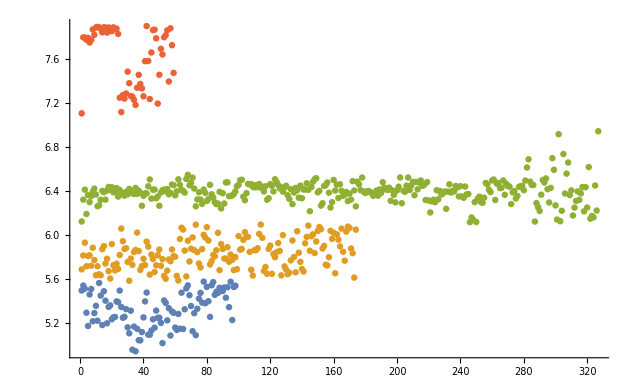

```mathematica
(* let also take a look on clustering attempt of Mathematica *)
ListPlot[FindClusters[entropies]]
```

```mathematica
Entropy[2,ExampleData[{"Text","ShakespearesSonnets"}]]//N
```

4.42366

```mathematica
input=BinaryReadList["C:\\P\\entropy\\wr941ndv5_en_3_15_9_up_boot(140627).bin"];
```

```mathematica
input=BinaryReadList["C:\\P\\entropy\\GeoIPISP.dat"];
```

```mathematica
input=BinaryReadList["C:\\P\\entropy\\notepad.exe"];
```